```mathematica
?FindFit
```

FindFit[data,expr,pars,vars] finds numerical values of the parameters pars that make expr give a best fit to data as a function of vars. The data can have the form {{x_1,y_1,…,f_1},{x_2,y_2,…,f_2},…}, where the number of coordinates x, y, … is equal to the number of variables in the list vars. The data can also be of the form {f_1,f_2,…}, with a single coordinate assumed to take values 1, 2, …. 
FindFit[data,{expr,cons},pars,vars] finds a best fit subject to the parameter constraints cons.

```mathematica
final=Table[{data[[i,2]],data[[i,2]]-data[[i+1,2]]},{i,1,Length[data],2}]
```

{{0.842687,0.00208092},{3.22658,0.00218511},{7.17422,0.002321},{12.6895,0.00256623},{19.7739,0.00296729},{28.4281,0.00357136},{38.6526,0.00441734},{50.4477,0.0055512},{63.8136,0.00701539},{78.7505,0.00885518},{95.2586,0.0111158},{113.338,0.0138419},{132.989,0.0170822},{154.212,0.0208849},{177.006,0.0252982},{201.372,0.0303741},{227.31,0.0361642},{254.82,0.0427233},{283.903,0.0501067},{314.558,0.0583733},{346.785,0.0675816},{380.585,0.0777957}}

```mathematica
ys=Table[final[[i]],{i,Length[final]}]
```

```mathematica
para=FindFit[Table[final[[i,1]],{i,Length[final]}],a x^2+b x+c,{a,b,c},x]
```

{a→0.785615,b→0.0123839,c→0.0633497}

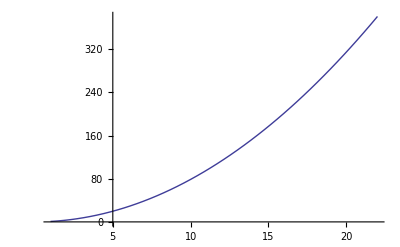

```mathematica
Plot[a x^2+b x+c/.para,{x,1,Length[final]}]
```

```mathematica
F[x_]=a x^2+b x+c/.para
```

0.0633497+0.0123839 x+0.785615 x^2

```mathematica
fitvals=Table[F[i],{i,1,Length[final]}];
```

```mathematica
residuals=Table[fitvals[[i]]-final[[i,1]],{i,1,Length[final]}]
```

{0.0186613,0.00399889,-0.00318707,-0.0068011,-0.00827602,-0.00834369,-0.00745186,-0.00591571,-0.00397531,-0.00182773,0.000356687,0.00242817,0.00424576,0.0056785,0.00660107,0.00689052,0.0064268,0.00509124,0.00276509,-0.000671334,-0.00533779,-0.0113564}

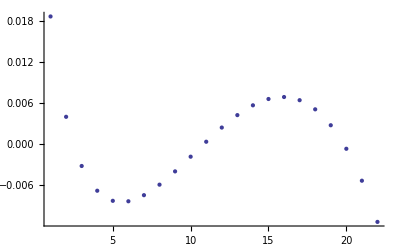

```mathematica
ListPlot[residuals]
```

```mathematica
Table[Abs[residuals[[i]]]<final[[i,2]],{i,1,Length[final]}]
```

{False,False,False,False,False,False,False,False,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### Loglog and other shenanigans

```mathematica
loglog=Table[{Log[N[i]],Log[final[[i,1]]],1/final[[i,1]]*final[[i,2]]},{i,1,Length[final]}];
```

```mathematica
test=LinearModelFit[Table[{loglog[[i,1]],loglog[[i,2]]},{i,Length[loglog]}],x,x]
```

FittedModel[-0.200233+1.98469 x]

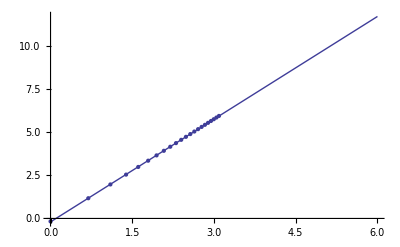

```mathematica
Show[Plot[Normal[test],{x,0,6}],ListPlot[Table[{loglog[[i,1]],loglog[[i,2]]},{i,Length[loglog]}]]]
```

```mathematica
F[x_]=Normal[test]
```

-0.200233+1.98469 x

```mathematica
fitvals=Table[F[loglog[[i,1]]],{i,1,Length[loglog]}];
```

```mathematica
fitvals
```

{-0.200233,1.17545,1.98017,2.55113,2.994,3.35585,3.66179,3.92681,4.16057,4.36968,4.55884,4.73153,4.89039,5.03747,5.1744,5.30249,5.42281,5.53625,5.64356,5.74536,5.8422,5.93452}

```mathematica
residuals=Table[fitvals[[i]]-loglog[[i,2]],{i,1,Length[loglog]}];
```

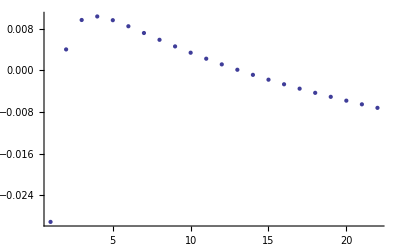

```mathematica
ListPlot[residuals]
```

```mathematica
Table[Abs[residuals[[i]]]<loglog[[i,3]],{i,1,Length[loglog]}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False}